# Bank statements analysis in Mathematica

In this file I am going to investigate my own outgoing expenses from my online banking. First I will import the first six months of 2017 as a comma-separated value (CSV) file. Second I will use some Mathematica built-in functions in order to classify my personal outgoing expenses. Such a classification will allows me to obtain the trend of each class. 

Note that this analysis is basically the same one for every class of my personal outgoing expenses. Thus, I will comment only the first class, i.e. Supermarket expenses.

## Importing CSV file and Visualization of my Dataset

Importing CSV file:

```mathematica
fileImp=Import["f5.csv"];
```

Dimension of data frame:

```mathematica
Dimensions[fileImp]
```

{193,4}

Data frame visualization:

```mathematica
Dataset[fileImp]
```

Dataset[<>]

```mathematica
Dimensions[Dataset[fileImp]]
```

{193,4}

Transforming our data frame into a list of associations and padding the associations with zeros where we have no values:

```mathematica
named = Map[AssociationThread[First[fileImp] -> PadRight[#, 4]] &, Rest[fileImp]];
```

## Selecting specific columns and changing date format

Selecting interested columns:

```mathematica
selectedColumns=named[[All,{"Buchungstag","Beguenstigter/Zahlungspflichtiger","Betrag"}]];
```

```mathematica
Dataset[selectedColumns]
```

Dataset[<>]

Changing date format from “Day.Month.Year” into “Day,Month,Year” in the date column:

```mathematica
Bstag=named[[All,{"Buchungstag"}]];
```

```mathematica
InterpDataE=Interpreter["StructuredDate", DateFormat->{"Day",".","Month",".","YearShort"}];
```

```mathematica
InterpDataE[Bstag];
```

Selecting the month and year from each element of date column and creating a new column in the data frame for each of them:

```mathematica
prova=MapAt[InterpDataE,selectedColumns,{1;;,1}];
```

```mathematica
InterpDataE2=Map[With[{d = #Buchungstag}, <|"month" -> d[[1, 2]], "year" -> d[[1, 1]], #|>] &, prova];
```

```mathematica
Dataset[InterpDataE2]
```

Dataset[<>]

## List of Month

In order to plot the following results I need to have a list of the first of six months

```mathematica
Months={1,2,3,4,5,6};
```

## Supermarket expenses

Let us focus on my supermarket expenses. This analysis takes into consideration the following four supermarkets: Rewe, Tegut, Karstadt, Netto. Such supermarkets are extracted by using the following command:

```mathematica
Supermarkets=Select[InterpDataE2,#[[4]]=="ALDI GmbH + Co. KG HANN.MUENDEN"||#[[4]]=="NETTO MARKEN-DISCOU."||#[[4]]=="tegut... gute Lebens"||#[[4]]=="REWE-Markt Moewes oHG"||#[[4]]=="KARSTADT WARENHAUS GMHB"&];
```

```mathematica
Dataset[Supermarkets]
```

Dataset[<>]

Number of lines in this new association:

```mathematica
M=Supermarkets[[All,"month"]];
```

```mathematica
Length[M]
```

31

Extracting relevant data for each month:

```mathematica
MM6=Select[Supermarkets,#[[1]]==6&];
MM5=Select[Supermarkets,#[[1]]==5&];
MM4=Select[Supermarkets,#[[1]]==4&];
MM3=Select[Supermarkets,#[[1]]==3&];
MM2=Select[Supermarkets,#[[1]]==2&];
MM1=Select[Supermarkets,#[[1]]==1&];
```

Computing the total amount of the column “Betrag” for each month:

```mathematica
SMM6=Total[MM6[[All,"Betrag"]]];
SMM5=Total[MM5[[All,"Betrag"]]];
SMM4=Total[MM4[[All,"Betrag"]]];
SMM3=Total[MM3[[All,"Betrag"]]];
SMM2=Total[MM2[[All,"Betrag"]]];
SMM1=Total[MM1[[All,"Betrag"]]];
```

Making a list of the sums above:

```mathematica
SMMN={SMM1,SMM2,SMM3,SMM4,SMM5,SMM6};
```

In order to plot “month vs total amount” for my supermarket expenses, I will use the built-in function “timeseries” on the two lists: SMMN, Months.

```mathematica
tsSupermarketsM=TimeSeries[SMMN,{Months}];
```

Here we plot our data by using listplot:

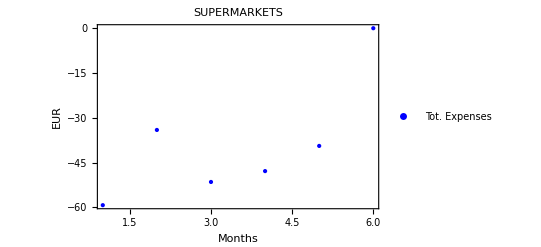

```mathematica
ListPlot[tsSupermarketsM,PlotRange->{All,All},PlotLegends->{"Tot. Expenses"},Frame->True,FrameLabel->{"Months",EUR },PlotStyle->{PointSize[Large],Blue},PlotLabel->"SUPERMARKETS"]
```

## Withdrawal expenses

Let us focus on my withdrawal expenses. This analysis takes into consideration all my withdrawals in the studied period of time.

```mathematica
Withdrawals=Select[InterpDataE2,#[[4]]=="GA NR00002257 BLZ26050001 0"||#[[4]]=="GA NR00002214 BLZ26050001 0"||#[[4]]=="GA NR00002218 BLZ26050001 0"||#[[4]]=="GA NR00002112 BLZ26050001 0"||#[[4]]=="GA NR00002170 BLZ26050001 0"&];
```

```mathematica
Dataset[Withdrawals]
```

Dataset[<>]

```mathematica
W=Withdrawals[[All,"month"]];
```

```mathematica
Length[W]
```

60

```mathematica
WW6=Select[Withdrawals,#[[1]]==6&];
WW5=Select[Withdrawals,#[[1]]==5&];
WW4=Select[Withdrawals,#[[1]]==4&];
WW3=Select[Withdrawals,#[[1]]==3&];
WW2=Select[Withdrawals,#[[1]]==2&];
WW1=Select[Withdrawals,#[[1]]==1&];
```

```mathematica
SWW6=Total[WW6[[All,"Betrag"]]];
SWW5=Total[WW5[[All,"Betrag"]]];
SWW4=Total[WW4[[All,"Betrag"]]];
SWW3=Total[WW3[[All,"Betrag"]]];
SWW2=Total[WW2[[All,"Betrag"]]];
SWW1=Total[WW1[[All,"Betrag"]]];
```

```mathematica
SWWN={SWW1,SWW2,SWW3,SWW4,SWW5,SWW6};
```

```mathematica
tsWithdrawalsM=TimeSeries[SWWN,{Months}];
```

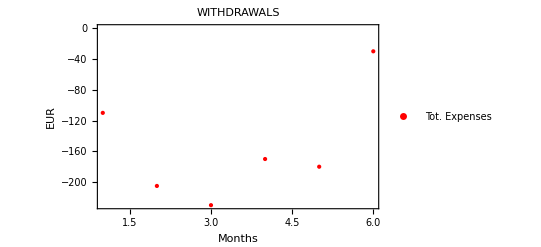

```mathematica
ListPlot[tsWithdrawalsM,PlotRange->{All,All},PlotLegends->{"Tot. Expenses"},Frame->True,FrameLabel->{"Months",EUR },PlotStyle->{PointSize[Large],Red},PlotLabel->"WITHDRAWALS"]
```

## Travel ticket expenses

Let us focus on my travel ticket expenses. This analysis takes into consideration all my tickets of trains and busses in the studied period of time.

```mathematica
TravelTicket=Select[InterpDataE2,#[[4]]=="PayPal Europe S.a.r.l. et Cie S.C.A"||#[[4]]=="DB Vertrieb GmnH"&];
```

```mathematica
Dataset[TravelTicket]
```

Dataset[<>]

```mathematica
T=TravelTicket[[All,"month"]];
```

```mathematica
Length[T]
```

11

```mathematica
TT6=Select[TravelTicket,#[[1]]==6&];
TT5=Select[TravelTicket,#[[1]]==5&];
TT4=Select[TravelTicket,#[[1]]==4&];
TT3=Select[TravelTicket,#[[1]]==3&];
TT2=Select[TravelTicket,#[[1]]==2&];
TT1=Select[TravelTicket,#[[1]]==1&];
```

```mathematica
STT6=Total[TT6[[All,"Betrag"]]];
STT5=Total[TT5[[All,"Betrag"]]];
STT4=Total[TT4[[All,"Betrag"]]];
STT3=Total[TT3[[All,"Betrag"]]];
STT2=Total[TT2[[All,"Betrag"]]];
STT1=Total[TT1[[All,"Betrag"]]];
```

```mathematica
STTN={STT1,STT2,STT3,STT4,STT5,STT6};
```

```mathematica
tsTravelTicketM=TimeSeries[STTN,{Months}];
```

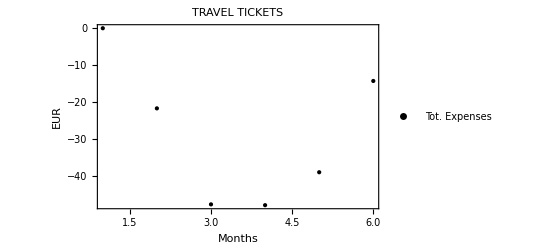

```mathematica
ListPlot[tsTravelTicketM,PlotRange->{All,All},PlotLegends->{"Tot. Expenses"},Frame->True,FrameLabel->{"Months",EUR },PlotStyle->{PointSize[Large],Black},PlotLabel->"TRAVEL TICKETS"]
```

## Rent expenses

Let us focus on my rent expenses. This analysis takes into consideration all rents in the studied period of time.

```mathematica
Rent=Select[InterpDataE2,#[[4]]=="MARTINA BONIFACI"&];
```

```mathematica
Dataset[Rent]
```

Dataset[<>]

```mathematica
R=Rent[[All,"month"]]
```

{5,4,3,3,2,1}

```mathematica
Length[R]
```

6

```mathematica
RR6=Select[Rent,#[[1]]==6&];
RR5=Select[Rent,#[[1]]==5&];
RR4=Select[Rent,#[[1]]==4&];
RR3=Select[Rent,#[[1]]==3&];
RR2=Select[Rent,#[[1]]==2&];
RR1=Select[Rent,#[[1]]==1&];
```

```mathematica
SRR6=Total[RR6[[All,"Betrag"]]];
SRR5=Total[RR5[[All,"Betrag"]]];
SRR4=Total[RR4[[All,"Betrag"]]];
SRR3=Total[RR3[[All,"Betrag"]]];
SRR2=Total[RR2[[All,"Betrag"]]];
SRR1=Total[RR1[[All,"Betrag"]]];
```

```mathematica
SRRN={SRR1,SRR2,SRR3,SRR4,SRR5,SRR6};
```

```mathematica
tsRentM=TimeSeries[SRRN,{Months}];
```

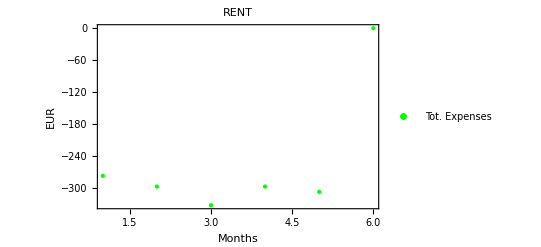

```mathematica
ListPlot[tsRentM,PlotRange->{All,All},PlotLegends->{"Tot. Expenses"},Frame->True,FrameLabel->{"Months",EUR },PlotStyle->{PointSize[Large],Green},PlotLabel->"RENT"]
```

## Visa card expenses

Let us focus on my visa card expenses. This analysis takes into consideration all uses of my visa card online or in direct payments in the studied period of time.

```mathematica
VisaCard=Select[InterpDataE2,#[[4]]=="FRANCESCO BERARDI"&];
```

```mathematica
Dataset[VisaCard]
```

Dataset[<>]

```mathematica
V=VisaCard[[All,"month"]]
```

{5,4,3,2,1,1}

```mathematica
Length[V]
```

6

```mathematica
VC6=Select[VisaCard,#[[1]]==6&];
VC5=Select[VisaCard,#[[1]]==5&];
VC4=Select[VisaCard,#[[1]]==4&];
VC3=Select[VisaCard,#[[1]]==3&];
VC2=Select[VisaCard,#[[1]]==2&];
VC1=Select[VisaCard,#[[1]]==1&];
```

```mathematica
SVC6=Total[VC6[[All,"Betrag"]]];
SVC5=Total[VC5[[All,"Betrag"]]];
SVC4=Total[VC4[[All,"Betrag"]]];
SVC3=Total[VC3[[All,"Betrag"]]];
SVC2=Total[VC2[[All,"Betrag"]]];
SVC1=Total[VC1[[All,"Betrag"]]];
```

```mathematica
SVCN={SVC1,SVC2,SVC3,SVC4,SVC5,SVC6};
```

```mathematica
tsVisaCardM=TimeSeries[SVCN,{Months}];
```

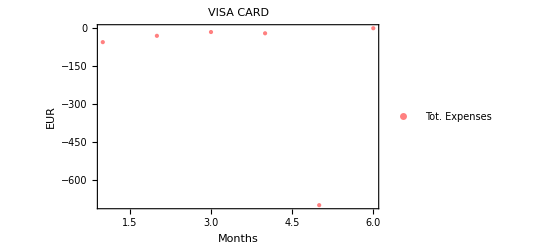

```mathematica
ListPlot[tsVisaCardM,PlotRange->{All,All},PlotLegends->{"Tot. Expenses"},Frame->True,FrameLabel->{"Months",EUR },PlotStyle->{PointSize[Large],Pink},PlotLabel->"VISA CARD"]
```

## All together

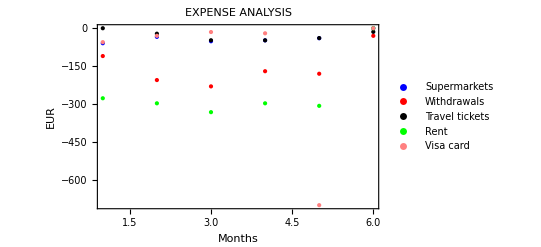

```mathematica
ListPlot[{tsSupermarketsM,tsWithdrawalsM,tsTravelTicketM,tsRentM,tsVisaCardM},PlotRange->{All,All},PlotLegends->{"Supermarkets","Withdrawals","Travel tickets","Rent","Visa card"},Frame->True,FrameLabel->{"Months",EUR },PlotStyle->{{PointSize[Large],Blue},{PointSize[Large],Red},{PointSize[Large],Black},{PointSize[Large],Green},{PointSize[Large],Pink}},PlotLabel->"EXPENSE ANALYSIS"]
```

```mathematica
ListPlot[{tsSupermarketsM,tsWithdrawalsM,tsTravelTicketM,tsRentM,tsVisaCardM},PlotRange->{All,{30,-370}},PlotLegends->{"Supermarkets","Withdrawals","Travel tickets","Rent","Visa card"},Frame->True,FrameLabel->{"Months",EUR },PlotStyle->{{PointSize[Large],Blue},{PointSize[Large],Red},{PointSize[Large],Black},{PointSize[Large],Green},{PointSize[Large],Pink}},PlotLabel->"EXPENSE ANALYSIS"]
```

-Graphics-

## Further Explorations

A further exploration would be cleaning this code and using many more built-in functions in order to make it more efficient and beautiful.

## Authorship information

Federico Dradi,
Friday, June 23rd 2017
federico.dradi@gmail.com